PM - Projekt autorstwa Pauliny Kulczyk, Jakuba Mieczkowskiego i Mateusza Madeja

# Gra w życie

## Historia ad 4), 6)

Gra w życie została wymyślona przez brytyjskiego matematyka Johna Conwaya. W 1970r. Martin Gardner (dziennikarz Scientific America, redaktor sekcji “Gry matematyczne”) dostał, jak zazwyczaj, list wypakowany pomysłami na kolejny artykuł. Wśród nich byl pewien 12 stronnicowy list. Jego 9 strona rozpoczynała aię donośnym nagłówkiem “The game of life”. Zawierała ona model matematyczny, który proponował spojrzenie na pewien automatyzm komórkowy. Zajmował się on proliferacją i wymieraniem pewnych swoiście określonych struktur komórkowych... Zaciekawiony Gardener postanowił przyjrzeć się głębiej zasadom gry. Gardener zdecydował się opublikować grę, ponieważ stwierdził że jest ona odniesieniem do narodzin i śmierci populacji żywych organizmów, nazwał to “symulacją życia”. Artykuł okazał się wielkim sukcesem a gra w życie zdobyła rzeszę fanów na całym świecie.
Warto dodać, że Conway uważał, że nie isnieje żadna struktura, która jest w stanie wyprodukować nieskończenie wiele komórek, czyli twierdził, że każda struktura po pewnej ilości iteracji ustabilizuje się, stanie się cyklem lub wygaśnie. Wyznaczył nawet nagrodę 50$ dla osoby, która znajdzie kontrprzykład obalający tą tezę przed końcem 1970r. Jednak okazało się, że w krótkim czasie znaleziono wiele kontrprzykładów.

## Zasady ad 1)

Zasady “Gry w życie są dość proste. Na poczatku nalezy wybrac pewne sekcje wypełnionych komórek, a nastepenie obserwować ich ewolucje na podstawie pewnych ustalonych zasad:
1. Zasada narodzin:  pusta (lub inaczej “umarła”) komórka staje się komórką pełną( lub inaczej “żywą”), jeżeli ma dokładnie 3 żywych sąsiadów (komórki, które mają wspólną krawędź lub wspólny wierzchołek).
2. Zasada śmierci:
- Z powodu izolacji: Żywa komórka staje się komorka martwa, jeżeli posiada 0 lub 1 sąsiada;
- Z powodu przeludnienia: Żywa komorka staje się komórką martwą, jeżeli posiada 4 lub więcej sąsiadów;
3. Zasada przeżycia: Żywa komórka z 2 lub 3 sąsiadami pozostaje komórką żywą.
Dzięki temu po każdej iteracji pewne komórki wymierają, pewne się rodzą, a pewne pozostają żywe [no coż, ŻYCIE!!!]
Poniżej przykład:

```mathematica
GameOfLife={224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
GraphicsGrid[{ArrayPlot[#,ImageSize->80,Mesh->True]&/@CellularAutomaton[GameOfLife,{{{0,1,0,1},{0,0,1,1},{1,1,1,0}},0},8]}]
```

-Graphics-

## Rodzaje struktur: ad 2)

1. Statyczne:
Struktura statyczna to taka, która nie zmienia swojego stanu początkowego (komórki żywe pozostają żywe, martwe pozostają martwe),
Na przykład:

```mathematica
GraphicsGrid[{ArrayPlot[#,ImageSize->50,Mesh->True]&/@CellularAutomaton[GameOfLife,{{{0,1,0},{1,0,1}, {1,0,1}, {0,1,0}},0},5]}]
```

-Graphics-

2. Oscylatory:
Struktury, które zmieniają się okresowo tworząc pewien powtarzający się cykl. Na przykład poniższa struktura jrest oscylatorem o okresie 2.

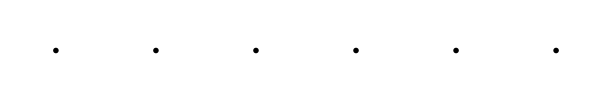

```mathematica
GraphicsGrid[{ArrayPlot[#,ImageSize->80,Mesh->True]&/@CellularAutomaton[GameOfLife,{{{0,0,1,1,1,0,0},{0,0,0,0,0,0,0},{1,0,0,0,0 ,0,1},{1,0,0,0,0 ,0,1}, {1,0,0,0,0 ,0,1},
{0,0,0,0,0,0,0}, {0,0,1,1,1,0,0}},0},5]}]
```

3. Statki:
Struktury, które poruszają się po polu “Gry w życie”, mając jednocześniei określony cykl.
Na przyklad, taki oto raczek:

```mathematica
Raczek = {{1, 1,1,0,0,0,0,0,0,0,0,0,0,1,1,1},{1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1},{1, 1,1,0,0,0,0,0,0,0,0,0,0,1,1,1}, {1,1,1,0,0,0,0,1,1,0,0,0,0,1,1,1}
{0,1,1,0,0,0,0,1,1,0,0,0,0,1,1,0}, {0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0}, {0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,0}, {0,0,0,1,1,1,1,1,1,1,1,1,1, 0 ,0,0}, {0,0,0,0,0,1,0,0,0,0,1,0,0, 0 ,0,0}, {0,0,0,0,0,1,0,0,0,0,1,0,0, 0 ,0,0}, {0,0,0,0,0,1,0,0,0,0,1,0,0, 0 ,0,0}}
```

{{1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1},{1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1},{1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1},{0,1,1,0,0,0,0,1,1,0,0,0,0,1,1,0},{0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,1,1,1,1,1,1,1,1,1,1,0,0,0},{0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0}}

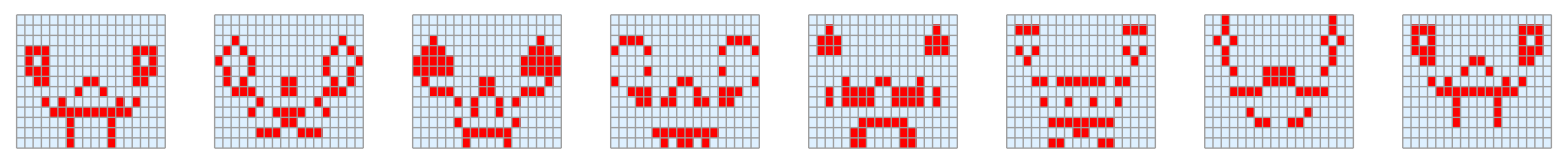

```mathematica
GraphicsGrid[{ArrayPlot[#,ImageSize->200,Mesh->True,  ColorRules -> {1-> Red, 0 -> LightBlue}]&/@CellularAutomaton[GameOfLife,{Raczek, 0},7]}]
```

4. Niestabilne:
Struktury, które nie spełniają powyższych zasad (nigdy nie wracają do swojej formy początkowej, czyli albo umierają albo stabilizują się po pewnym czasie przyjmując inna strukturę niż wyjściowa).

```mathematica
GraphicsGrid[{ArrayPlot[#,ImageSize->50,Mesh->True]&/@CellularAutomaton[GameOfLife,{{{0,1,0,1, 0},{0,1,1,1,0}, {0,0,0,0,0}},0}, 5]}]
```

-Graphics-

Uwaga: Istnieją wyjątkowe struktury niestabilne, które nie powstają w wyniku ewolucji jakiejkolwiek struktury. Jak dotąd odkryto bardzo niewiele takich styruktur. Najmniejsza z nich składa się ze 100 komórek.

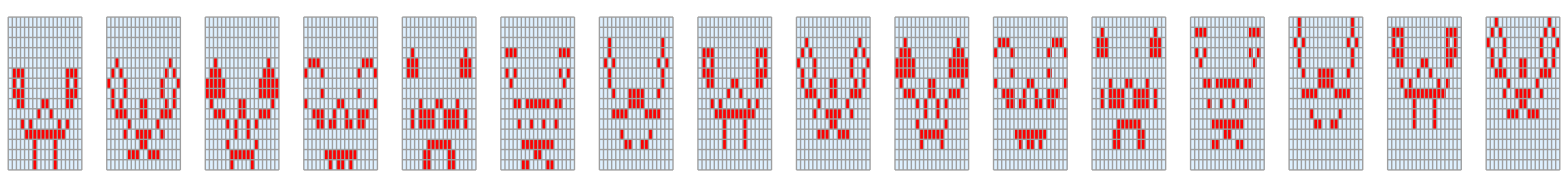

```mathematica
GraphicsGrid[{ArrayPlot[#,ImageSize->200,Mesh->True,  ColorRules -> {1-> Red, 0 -> LightBlue}]&/@CellularAutomaton[GameOfLife,{Raczek, 0},15]} ]
```

## funkcje potrzebne w czasie projektu

CellularAutomaton - funkcja, która pozwala na wyprodukowanie macierzy, kolejnych ewolucji komórek. Jako zmienne przyjmuje regułę - w naszym przypadku jest to zmienna GameOfLife - metoda zdefiniowana w bibliotekach Mathematici jako “Gra w życie”, macierz początkową - definiuje, które komórki będą żywe w 0-owej iteracji naszej procedury, ilość iteracji - liczba pokoleń

ArrayPlot - za pomocą tej funkcji, wizualizujemy macierz binarną jako szachownicę, w której zamalowane pola odpowiadają “1” w macierzy (żywe komórki), a pola białe “0” (martwe komórki). Funkcja daje nam również możliwość edycji wybranych elementów szachownicy.

GraphicsGrid - funkcja ta pozwala nam zwrócić kilka generacji szachownic wyprodukowanych w ArrayPlocie.

Manipulate - funkcja, dzięki której będziemy mogli zanimować przekształcenia naszych szachownic.

Show - Wraz z funkcją manipulate pozwala nam przedstawić tę animację na jednym wykresie.

## Propozycje testów programistycznych:

Spróbujemy zwizualizować bardziej skomplikowane przykłady oparte na rozbudowanych macierzach początkowych. (np “bitwy kosmiczne”, “life in life”, zegar zaimplementowany w grze w życie itp - jeszcze zdecydujemy) :)

## Ciekawe implementacje gry: ad5)

Aby pokazać bardziej złożone implementacje w przejrzysty sposób wykorzystamy funkcje manipulate. Zobaczmy jak będzie wyglądał raczek ad 3) ukazany za pomocą tej funkcji:

```mathematica
Manipulate[Labeled[Show[ArrayPlot[#,ImageSize->200,Mesh->True,ColorRules->{1->Red,0->LightBlue}]&/@CellularAutomaton[GameOfLife,{Raczek,0},t]],"Raczek"],{t,0,15,1}]
```

Możemy również za pomocą tej samej funkcji obejrzeć kolejne kroki implementacji gry w życie koło siebie (można np. sprawdzić czy faktycznie funkcja dobrze działa):

```mathematica
Manipulate[Labeled[GraphicsGrid[{ArrayPlot[#,ImageSize->200,Mesh->True,ColorRules->{1->Red,0->LightBlue}]&/@CellularAutomaton[GameOfLife,{Raczek,0},Step]}],"Raczek"],{Step,{0,1,2,3,4,5}}]
```

Dużą grupę implementacji stanowią oscylatory. Interesującymi przykładami takiej struktury są nożyczki :

```mathematica
Manipulate[Labeled[Show[ArrayPlot[#,ImageSize->400,Mesh->True,  ColorRules -> {1-> Red, 0 -> LightBlue}]&/@CellularAutomaton[GameOfLife,{scissors, 0},t]],"scissors"],{t,0,25,1}]
```

oraz młyn:

```mathematica
Manipulate[Labeled[Show[ArrayPlot[#,ImageSize->400,Mesh->True,  ColorRules -> {1-> Darker[Brown], 0 -> LightBlue}]&/@CellularAutomaton[GameOfLife,{Mlyn, 0},t]],"Mill"],{t,0,25,1}]
```

Inną liczną grupę rozbudowanych struktur, którą chcielibyśmy przedstawić, stanowią statki (“gliders”). Oto przemieszczające się w lewo struktury:

```mathematica
Manipulate[Labeled[Show[ArrayPlot[#,ImageSize->400,Mesh->True,  ColorRules -> {1-> RGBColor[0.97,0.47,0.38], 0 -> LightBlue}]&/@CellularAutomaton[GameOfLife,{Plywak, 0},t]],"Swimmer"],{t,0,20,1}]
```

Kolejnym ciekawym przykładem gry jest “Gosper glider gun”. Jest to taki statek strzelający gliderami. My postanowiliśmy zrobić implementacje, w której 2 statki strzelają do siebie, a ich pociski się wzajemnie niszczą.

```mathematica
Manipulate[Labeled[Show[ArrayPlot[#,ImageSize->500,Mesh->True,  ColorRules -> {1-> Black, 0 -> LightYellow}]&/@CellularAutomaton[GameOfLife,{wojnastatkow, 0},t]],"Gosper greeder gun"],{t,0,250,1}]
```

## Bibliografia:

https://www.google.pl/amp/s/www.nytimes.com/2020/12/28/science/math-conway-game-of-life.amp.html

https://www.sadistic.pl/gra-w-zycie-vt132225.htm

https://beltoforion.de/en/game_of_life/

https://mathworld.wolfram.com/GameofLife.html

https://playgameoflife.com/ → symulator internetowy, można samemu tworzyć swoje unikalne struktury ;)

https://www.youtube.com/watch?v=R9Plq-D1gEk → bardzo fajny wywiad

## Dane do rozbudowanych struktur

```mathematica
scissors={{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,1,0,1,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0},{1,1,0,0,1,0,0,0,0,1,0,0,1,1,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0},{0,1,0,0,1,0,1,1,0,1,0,0,1,0,0,0,1,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0}}
```

```mathematica
Mlyn={{0,0,0,0,0,0,1,0,0,0},{0,1,1,0,1,0,1,0,0,0},{0,1,0,0,0,0,0,0,1,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1},{0,1,0,1,0,0,0,0,0,0},{0,1,1,0,0,1,0,1,0,0},{0,0,0,0,0,1,0,0,0,0}};
```

```mathematica
Plywak={{0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,1,1,1,0},{0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,1,1,0,0,0,0,0},{0,1,1,1,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
wojnastatkow=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 1, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 1, 0, 1, 1, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 1, 1, 0, 1, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 1, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});
```